### Einzelmessung

```mathematica
Clear[RiV, UV, IA]
R[U_,I_] := U /(I - U/RiV)
du = D[R[UV,IA],UV ]//FullSimplify
di = D[R[UV,IA],IA] //FullSimplify
UV = 4.852;
IA = 0.07141;
RiV =10000000;
{du,di}
```

(IA RiV^2)/(-IA RiV+UV)^2

-UV/(IA-UV/RiV)^2

{14.0038,-951.5}

### Glühdraht

```mathematica
Clear[α,β,R0, θ0]
R[θ_] := R0(1+α(θ-θ0)+β(θ-θ0)^2)
InverseFunction[R]//FullSimplify
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

(-R0 α+2 R0 β θ0-√R0 √(R0 α^2-4 R0 β+4 β #1))/(2 R0 β)&

```mathematica
α = 4.1*10^(-3);
β = 1.0*10^(-6);
R0 = 30.39;
θ0 = 20;
data = {
197.6344928,
286.2022208,
342.4816085,
395.1312935,
442.0649958,
481.3619122
};
temp = Table[NSolve[R[θ]==d,θ, PositiveReals],{d,data}] // Flatten
```

{θ→1085.41,θ→1522.48,θ→1774.21,θ→1995.48,θ→2182.94,θ→2333.71}

### 2: AC-DC Kopplung

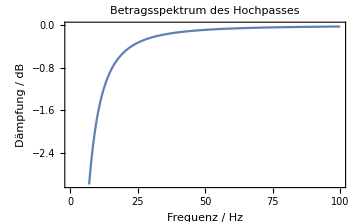

```mathematica
Plot[20*Log10[Abs[1/(1+7/(ⅈ*f))]],{f,1, 100},
PlotLabel->Style["Betragsspektrum des Hochpasses",FontWeight->Bold, FontSize->14],
Frame -> True,
PlotRange->{{0,100},{-3,0}},
FrameLabel->{Style["Frequenz / Hz", FontSize->14],Style[ "Dämpfung / dB", FontSize->12]},
ImageSize->Medium
]
```